```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,8000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ},{0.-22.3585 ⅈ,1.+0. ⅈ,0.+9.26116 ⅈ,0.+0. ⅈ,0.+9.26121 ⅈ,0.+0. ⅈ,0.-22.3585 ⅈ},{-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ},{«1»},{2.5×10^7+0. ⅈ,«5»,-2.5×10^7+«1»},{0.-22.3585 ⅈ,0.+0. ⅈ,0.+9.26121 ⅈ,0.+0. ⅈ,0.+9.26116 ⅈ,1.+0. ⅈ,0.-22.3585 ⅈ},{-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ},{0.-63.6174 ⅈ,1.+0. ⅈ,0.+26.3512 ⅈ,0.+0. ⅈ,0.+26.3512 ⅈ,0.+0. ⅈ,0.-63.6174 ⅈ},{-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ},{«1»},{2.5×10^7+0. ⅈ,«5»,-2.5×10^7+0. ⅈ},{0.-63.6174 ⅈ,0.+0. ⅈ,0.+26.3512 ⅈ,0.+0. ⅈ,0.+26.3512 ⅈ,1.+0. ⅈ,0.-63.6174 ⅈ},{-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ},{0.-173.447 ⅈ,1.+0. ⅈ,0.+71.8439 ⅈ,0.+0. ⅈ,0.+71.844 ⅈ,0.+0. ⅈ,0.-173.447 ⅈ},{-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ},{«1»},{2.5×10^7+0. ⅈ,«5»,-2.5×10^7+0. ⅈ},{0.-173.447 ⅈ,0.+0. ⅈ,0.+71.844 ⅈ,0.+0. ⅈ,0.+71.8439 ⅈ,1.+0. ⅈ,0.-173.447 ⅈ},{-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ,0.+0. ⅈ,-2.5×10^7+0. ⅈ,0.+0. ⅈ,2.5×10^7+0. ⅈ}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

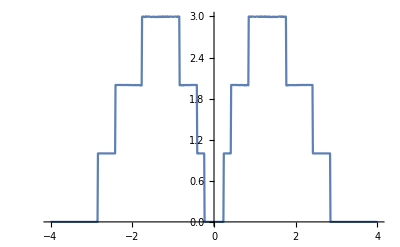

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}];Clear[imp1,imp2,imp3,imp7,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.0001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.0001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,0.0001,1,0,ϵ1].T1[1].SL[ω,0.0001,1,0].T1[1]].imp1[ω,0.0001,1,0,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,0.0001,1,0,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,0.0001,1,0,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,0.0001,1,0,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,0.0001,1,0,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp7[ω,0.0001,1,0,ϵ1].T2[1].Sl13.T2[1]].imp7[ω,0.0001,1,0,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,0.0001,1,0,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,0.0001,1,0,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,0.0001,1,0,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,0.0001,1,0,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,0.0001,1,0,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,0.0001,1,0,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,0.0001,1,0,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,0.0001,1,0,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Print[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8];m1=Table[{ω,If[ψ[ω,0.0001,1,0,0.6]>3,3,ψ[ω,0.0001,1,0,0.6]]},{ω,Range[0,4,0.01]}]
```

65766556

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}];Clear[imp1,imp2,imp3,imp7,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.0001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.0001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,0.0001,1,0,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,0.0001,1,0,ϵ1].T1[1].SL[ω,0.0001,1,0].T1[1]].imp1[ω,0.0001,1,0,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,0.0001,1,0,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,0.0001,1,0,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,0.0001,1,0,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,0.0001,1,0,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp7[ω,0.0001,1,0,ϵ1].T2[1].Sl13.T2[1]].imp7[ω,0.0001,1,0,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,0.0001,1,0,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,0.0001,1,0,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,0.0001,1,0,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,0.0001,1,0,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,0.0001,1,0,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,0.0001,1,0,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,0.0001,1,0,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,0.0001,1,0,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];E=0.5 vPrint[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8];m3=Table[{ω,If[ψ[ω,0.0001,1,0,0.6]>3,3,ψ[ω,0.0001,1,0,0.6]]},{ω,Range[0,4,0.01]}]
```

62242722

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}];Clear[imp1,imp2,imp3,imp7,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.0001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,0.0001,1,0,ϵ1].T1[1].SL[ω,0.0001,1,0].T1[1]].imp1[ω,0.0001,1,0,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,0.0001,1,0,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,0.0001,1,0,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,0.0001,1,0,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,0.0001,1,0,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp7[ω,0.0001,1,0,ϵ1].T2[1].Sl13.T2[1]].imp7[ω,0.0001,1,0,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,0.0001,1,0,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,0.0001,1,0,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,0.0001,1,0,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,0.0001,1,0,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,0.0001,1,0,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,0.0001,1,0,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,0.0001,1,0,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,0.0001,1,0,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Print[{μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8}];m4=Table[{ω,If[ψ[ω,0.0001,1,0,0.6]>3,3,ψ[ω,0.0001,1,0,0.6]]},{ω,Range[0,4,0.01]}]
```

{6,6,1,2,3,7,5,4}

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}];Clear[imp1,imp2,imp3,imp7,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.0001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,0.0001,1,0,ϵ1].T1[1].SL[ω,0.0001,1,0].T1[1]].imp1[ω,0.0001,1,0,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,0.0001,1,0,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,0.0001,1,0,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,0.0001,1,0,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,0.0001,1,0,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp7[ω,0.0001,1,0,ϵ1].T2[1].Sl13.T2[1]].imp7[ω,0.0001,1,0,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,0.0001,1,0,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,0.0001,1,0,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,0.0001,1,0,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,0.0001,1,0,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,0.0001,1,0,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,0.0001,1,0,ϵ1];E=0.5 v
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,0.0001,1,0,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,0.0001,1,0,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Print[{μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8}];m5=Table[{ω,If[ψ[ω,0.0001,1,0,0.6]>3,3,ψ[ω,0.0001,1,0,0.6]]},{ω,Range[0,4,0.01]}]
```

{7,7,2,3,3,3,2,2}

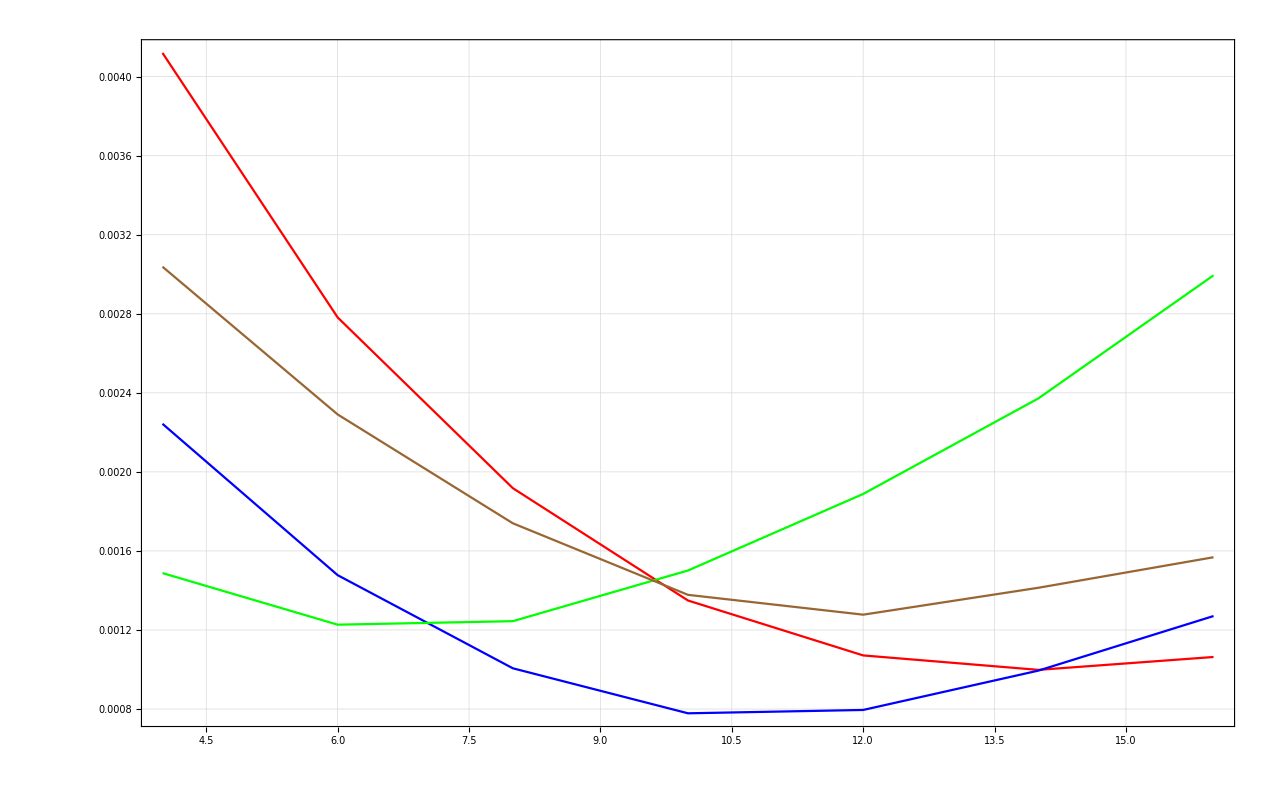

```mathematica
Show[ListLinePlot[{{4,Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/new/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/new/3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{8,Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/new/4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{10,Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/new/5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{12,Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/new/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{14,Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/new/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{16,Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]-Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/new/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]}},PlotTheme->"Detailed",PlotStyle->Red],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],1/(m1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/new/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/new/3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/new/4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/new/5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/new/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/new/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]-Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/new/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]}},PlotTheme->"Detailed",PlotStyle->Blue],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/new/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/new/3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/new/4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/new/5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/new/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/new/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]-Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/new/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]}},PlotTheme->"Detailed",PlotStyle->Green],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/new/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/new/3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/new/4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/new/5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/new/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/new/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]-Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/new/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]}},PlotTheme->"Detailed",PlotStyle->Brown],PlotRange->All]
```

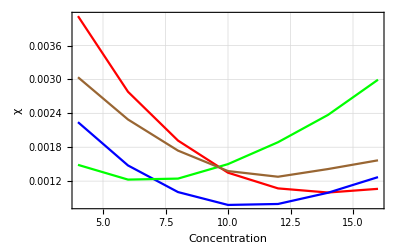

```mathematica
Show[%38,FrameLabel->{{HoldForm[χ],None},{HoldForm[Concentration],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

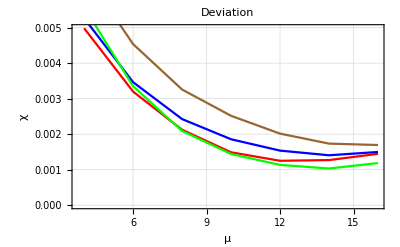

```mathematica
Show[%190,FrameLabel->{{HoldForm[χ],None},{HoldForm[μ],None}},PlotLabel->HoldForm[Deviation],LabelStyle->{GrayLevel[0]}]
```

```mathematica
υ[ϵ1_,τ_]:=Module[{μ1=RandomInteger[{1,7}],μ2=RandomInteger[{1,7}],μ3=RandomInteger[{1,7}],μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}],μ6=RandomInteger[{1,7}],μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}]},
η:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]];imp5=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.0001-0]]];imp5=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.0001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[7]-imp5.T2[1].Sl15.T2[1]].imp5;Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]];Clear[m5];m5:=m5=Table[{ω,η},{ω,Range[0,4,0.01]}];ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8}};Min[list]]
```

```mathematica
υ[ϵ1_,x_,y_]:=Module[{μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}], μ9=RandomInteger[{4,7}], μ10=RandomInteger[{4,7}], μ11=RandomInteger[{4,7}]
(*Print[{μ1,μ2,μ3,μ5,μ6,μ8}]*)},
η5:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.0001-0]]];imp7=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.0001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Clear[m5];
m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11},{12,ρ12}};Print[list];{list[[Position[list,Min[list]][[1,1]],1]],Min[list],Show[ListLinePlot[m5],%24],
{μ1,μ3,μ5,μ8},{μ1+μ3+μ5+μ8}}]
```

```mathematica
υ[0.7,1.4,0.9]
```

{{2,0.000103802},{3,0.000491721},{4,0.000256565},{5,0.000219861},{6,0.000363244},{7,0.000621988},{8,0.000961648},{9,0.000512782},{10,0.000174098},{11,0.00218235},{12,0.00260091}}

```mathematica
μ1=RandomInteger[{1,7}]; μ2=RandomInteger[{1,7}]; μ3=RandomInteger[{1,7}]; μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}]; μ6=RandomInteger[{1,7}]; μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
κ27:=κ27=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"]
```

```mathematica
κ37:=κ37=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"]
```

```mathematica
κ47:=κ47=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"]
```

```mathematica
κ57:=κ57=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"]
```

```mathematica
κ67:=κ67=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"]
```

```mathematica
κ77:=κ77=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"]
```

```mathematica
κ87:=κ87=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"]
```

```mathematica
κ97:=κ97=Import["/home/shardulmukim/9imp7.csv"]
```

```mathematica
κ107:=κ107=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"]
```

```mathematica
κ117:=κ117=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"]
```

```mathematica
κ127:=κ127=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"]
```

```mathematica
υ[ϵ1_,x_,y_]:=Module[{},
η5:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]];imp5=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.0001-0]]];imp7=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Clear[m5];
m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ27[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ37[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ47[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ57[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ67[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ77[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ87[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ97[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ107[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ117[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ127[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10,ρ11,ρ12};(*Print[list];*)Min[list](*list[[Position[list,Min[list]][[1,1]],1]],Min[list]*)(*,ListLinePlot[m5],
{μ3,μ4,μ5,μ6}*)(*,{μ1+μ3+μ5+μ8}*)]
```

```mathematica
υ[0.7,1.75,0]
```

$Aborted

```mathematica
f[0.85]
```

{{0.1,0.0000142038},{0.11,0.0000147972},{0.12,0.0000153727},{0.13,0.0000157315},{0.14,0.0000158564},{0.15,0.0000157948},{0.16,0.0000156699},{0.17,0.0000156409},{0.18,0.0000159033},{0.19,0.0000170925},{0.2,0.0000191843},{0.21,0.0000221642},{0.22,0.0000280864},{0.23,0.0000410167},{0.24,0.0000535574},{0.25,0.0000567019},{0.26,0.0000560588},{0.27,0.0000564345},{0.28,0.0000575959},{0.29,0.0000586409},{0.3,0.0000592059},{0.31,0.0000595522},{0.32,0.0000597573},{0.33,0.0000596671},{0.34,0.0000593647},{0.35,0.0000590025},{0.36,0.0000585423},{0.37,0.0000583348},{0.38,0.0000585465},{0.39,0.0000588632},{0.4,0.0000596232},{0.41,0.0000615066},{0.42,0.0000633322},{0.43,0.0000648088},{0.44,0.0000665352},{0.45,0.0000686333},{0.46,0.0000708684},{0.47,0.0000720575},{0.48,0.0000735076},{0.49,0.0000747437},{0.5,0.0000757439},{0.51,0.0000773711},{0.52,0.0000786856},{0.53,0.0000797509},{0.54,0.0000800678},{0.55,0.0000796879},{0.56,0.0000792791},{0.57,0.0000788824},{0.58,0.0000784111},{0.59,0.0000779787},{0.6,0.0000775107},{0.61,0.000077035},{0.62,0.0000765186},{0.63,0.0000760088},{0.64,0.0000755341},{0.65,0.0000750986},{0.66,0.0000747419},{0.67,0.0000746485},{0.68,0.0000746079},{0.69,0.0000745455},{0.7,0.0000745988},{0.71,0.0000747067},{0.72,0.0000753626},{0.73,0.000076612},{0.74,0.0000780792},{0.75,0.0000803034},{0.76,0.0000830434},{0.77,0.0000857957},{0.78,0.0000889728},{0.79,0.0000924921},{0.8,0.0000960148},{0.81,0.0000992263},{0.82,0.000101919},{0.83,0.000103963},{0.84,0.000105475},{0.85,0.000106403},{0.86,0.000106988},{0.87,0.000107349},{0.88,0.000107101},{0.89,0.000106528},{0.9,0.00010605},{0.91,-0.000198437},{0.92,0.00389368},{0.93,0.00801525},{0.94,0.00786948},{0.95,0.00787979},{0.96,0.00792918},{0.97,0.00795058},{0.98,0.00794992},{0.99,0.00793742},{1.,0.00790868},{1.01,0.00786924},{1.02,0.00782727},{1.03,0.00778667},{1.04,0.00774745},{1.05,0.00770942},{1.06,0.00767305},{1.07,0.00763749},{1.08,0.00760226},{1.09,0.00756638},{1.1,0.00752979},{1.11,0.00749321},{1.12,0.0074565},{1.13,0.00741979},{1.14,0.00738294},{1.15,0.00734613},{1.16,0.0073096},{1.17,0.00727346},{1.18,0.0072378},{1.19,0.00720275},{1.2,0.00716842},{1.21,0.00713469},{1.22,0.00710157},{1.23,0.00706954},{1.24,0.00703843},{1.25,0.00700812},{1.26,0.00697886},{1.27,0.00694992},{1.28,0.0069217},{1.29,0.00689464},{1.3,0.00686785},{1.31,0.00684123},{1.32,0.00681489},{1.33,0.0067889},{1.34,0.00676287},{1.35,0.00673671},{1.36,0.00671063},{1.37,0.00668476},{1.38,0.00665907},{1.39,0.00663299},{1.4,0.00660661},{1.41,0.00658035},{1.42,0.00655407},{1.43,0.00652733},{1.44,0.00650063},{1.45,0.0064742},{1.46,0.00644753},{1.47,0.00642054},{1.48,0.00639353},{1.49,0.00636652},{1.5,0.00633949},{1.51,0.00631265},{1.52,0.0062862},{1.53,0.0062604},{1.54,0.00623529},{1.55,0.00620939},{1.56,0.00618306},{1.57,0.00609954},{1.58,0.00834167},{1.59,0.0119632},{1.6,0.0131408},{1.61,0.0129924},{1.62,0.0129519},{1.63,0.0128989},{1.64,0.0128482},{1.65,0.0128056},{1.66,0.012764},{1.67,0.0127155},{1.68,0.0126658},{1.69,0.0126161},{1.7,0.0125667},{1.71,0.0125178},{1.72,0.0124697},{1.73,0.0124226},{1.74,0.0123766},{1.75,0.0123318},{1.76,0.0122884},{1.77,0.0122463},{1.78,0.0122053},{1.79,0.0121654},{1.8,0.0121262},{1.81,0.0120876},{1.82,0.0120497},{1.83,0.0120123},{1.84,0.0119751},{1.85,0.0119378},{1.86,0.0119005},{1.87,0.0118627},{1.88,0.0118242},{1.89,0.0117845},{1.9,0.0117435},{1.91,0.0117017},{1.92,0.0116595},{1.93,0.0116178},{1.94,0.0115769},{1.95,0.0115364},{1.96,0.0114958},{1.97,0.011455},{1.98,0.0114157},{1.99,0.011369},{2.,0.0112986},{2.01,0.0130783},{2.02,0.0147257},{2.03,0.0145036},{2.04,0.0151437},{2.05,0.0157768},{2.06,0.0156703},{2.07,0.0156174},{2.08,0.0155648},{2.09,0.0155123},{2.1,0.0154599},{2.11,0.0154077},{2.12,0.0153559},{2.13,0.0153043},{2.14,0.0152531},{2.15,0.0152023},{2.16,0.0151518},{2.17,0.0151016},{2.18,0.0150518},{2.19,0.0150023},{2.2,0.0149531},{2.21,0.0149042},{2.22,0.0148557},{2.23,0.0148074},{2.24,0.0147595},{2.25,0.0147119},{2.26,0.0146646},{2.27,0.0146176},{2.28,0.0145709},{2.29,0.0145245},{2.3,0.0144784},{2.31,0.0144326},{2.32,0.014387},{2.33,0.0143418},{2.34,0.0142968},{2.35,0.0142522},{2.36,0.0142078},{2.37,0.0141636},{2.38,0.0141198},{2.39,0.0140762},{2.4,0.0140329},{2.41,0.0139899},{2.42,0.0139471},{2.43,0.0139046},{2.44,0.0138623},{2.45,0.0138203},{2.46,0.0137785},{2.47,0.013737},{2.48,0.0136958},{2.49,0.0136548},{2.5,0.013614},{2.51,0.0135735},{2.52,0.0135332},{2.53,0.0134932},{2.54,0.0134534},{2.55,0.0134138},{2.56,0.0133745},{2.57,0.0133354},{2.58,0.0132965},{2.59,0.0132578},{2.6,0.0132194},{2.61,0.0131812},{2.62,0.0131432},{2.63,0.0131054},{2.64,0.0130679},{2.65,0.0130306},{2.66,0.0129934},{2.67,0.0129565},{2.68,0.0129198},{2.69,0.0128833},{2.7,0.012847},{2.71,0.0128109},{2.72,0.0127751},{2.73,0.0127394},{2.74,0.0127039},{2.75,0.0126686},{2.76,0.0126335},{2.77,0.0125986},{2.78,0.0125639},{2.79,0.0125294},{2.8,0.012495},{2.81,0.0124609},{2.82,0.012427},{2.83,0.0123932},{2.84,0.0123596},{2.85,0.0123262},{2.86,0.012293},{2.87,0.0122599},{2.88,0.0122271},{2.89,0.0121944},{2.9,0.0121618},{2.91,0.0121295},{2.92,0.0120973},{2.93,0.0120653},{2.94,0.0120335},{2.95,0.0120018},{2.96,0.0119703},{2.97,0.011939},{2.98,0.0119078},{2.99,0.0118768},{3.,0.011846},{3.01,0.0118153},{3.02,0.0117847},{3.03,0.0117544},{3.04,0.0117241},{3.05,0.0116941}}

{{2.05,0.0157768},{2.06,0.0156703},{2.07,0.0156174},{2.08,0.0155648},{2.09,0.0155123},{2.1,0.0154599},{2.11,0.0154077},{2.12,0.0153559},{2.13,0.0153043},{2.14,0.0152531},{2.15,0.0152023},{2.16,0.0151518},{2.17,0.0151016},{2.18,0.0150518},{2.19,0.0150023},{2.2,0.0149531},{2.21,0.0149042},{2.22,0.0148557},{2.23,0.0148074},{2.24,0.0147595},{2.25,0.0147119},{2.26,0.0146646},{2.27,0.0146176},{2.28,0.0145709},{2.29,0.0145245},{2.3,0.0144784},{2.31,0.0144326},{2.32,0.014387},{2.33,0.0143418},{2.34,0.0142968},{2.35,0.0142522},{2.36,0.0142078},{2.37,0.0141636},{2.38,0.0141198},{2.39,0.0140762},{2.4,0.0140329},{2.41,0.0139899},{2.42,0.0139471},{2.43,0.0139046},{2.44,0.0138623},{2.45,0.0138203},{2.46,0.0137785},{2.47,0.013737},{2.48,0.0136958},{2.49,0.0136548},{2.5,0.013614},{2.51,0.0135735},{2.52,0.0135332},{2.53,0.0134932},{2.54,0.0134534},{2.55,0.0134138},{2.56,0.0133745},{2.57,0.0133354},{2.58,0.0132965},{2.59,0.0132578},{2.6,0.0132194},{2.61,0.0131812},{2.62,0.0131432},{2.63,0.0131054},{2.64,0.0130679},{2.65,0.0130306},{2.66,0.0129934},{2.67,0.0129565},{2.68,0.0129198},{2.69,0.0128833},{2.7,0.012847},{2.71,0.0128109},{2.72,0.0127751},{2.73,0.0127394},{2.74,0.0127039},{2.75,0.0126686},{2.76,0.0126335},{2.77,0.0125986},{2.78,0.0125639},{2.79,0.0125294},{2.8,0.012495},{2.81,0.0124609},{2.82,0.012427},{2.83,0.0123932},{2.84,0.0123596},{2.85,0.0123262},{2.86,0.012293},{2.87,0.0122599},{2.88,0.0122271},{2.89,0.0121944},{2.9,0.0121618},{2.91,0.0121295},{2.92,0.0120973},{2.93,0.0120653},{2.94,0.0120335},{2.95,0.0120018},{2.96,0.0119703},{2.97,0.011939},{2.98,0.0119078},{2.99,0.0118768},{3.,0.011846},{3.01,0.0118153},{3.02,0.0117847},{3.03,0.0117544},{3.04,0.0117241},{3.05,0.0116941}}

```mathematica
Transpose[%95]
```

{{2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,2.21,2.22,2.23,2.24,2.25,2.26,2.27,2.28,2.29,2.3,2.31,2.32,2.33,2.34,2.35,2.36,2.37,2.38,2.39,2.4,2.41,2.42,2.43,2.44,2.45,2.46,2.47,2.48,2.49,2.5,2.51,2.52,2.53,2.54,2.55,2.56,2.57,2.58,2.59,2.6,2.61,2.62,2.63,2.64,2.65,2.66,2.67,2.68,2.69,2.7,2.71,2.72,2.73,2.74,2.75,2.76,2.77,2.78,2.79,2.8,2.81,2.82,2.83,2.84,2.85,2.86,2.87,2.88,2.89,2.9,2.91,2.92,2.93,2.94,2.95,2.96,2.97,2.98,2.99,3.,3.01,3.02,3.03,3.04,3.05},{0.0157768,0.0156703,0.0156174,0.0155648,0.0155123,0.0154599,0.0154077,0.0153559,0.0153043,0.0152531,0.0152023,0.0151518,0.0151016,0.0150518,0.0150023,0.0149531,0.0149042,0.0148557,0.0148074,0.0147595,0.0147119,0.0146646,0.0146176,0.0145709,0.0145245,0.0144784,0.0144326,0.014387,0.0143418,0.0142968,0.0142522,0.0142078,0.0141636,0.0141198,0.0140762,0.0140329,0.0139899,0.0139471,0.0139046,0.0138623,0.0138203,0.0137785,0.013737,0.0136958,0.0136548,0.013614,0.0135735,0.0135332,0.0134932,0.0134534,0.0134138,0.0133745,0.0133354,0.0132965,0.0132578,0.0132194,0.0131812,0.0131432,0.0131054,0.0130679,0.0130306,0.0129934,0.0129565,0.0129198,0.0128833,0.012847,0.0128109,0.0127751,0.0127394,0.0127039,0.0126686,0.0126335,0.0125986,0.0125639,0.0125294,0.012495,0.0124609,0.012427,0.0123932,0.0123596,0.0123262,0.012293,0.0122599,0.0122271,0.0121944,0.0121618,0.0121295,0.0120973,0.0120653,0.0120335,0.0120018,0.0119703,0.011939,0.0119078,0.0118768,0.011846,0.0118153,0.0117847,0.0117544,0.0117241,0.0116941}}

```mathematica
{%150[[1]]-1,%150[[2]]/20}
```

{{1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.,2.01,2.02,2.03,2.04,2.05},{0.000788839,0.000783516,0.000780869,0.000778242,0.000775617,0.000772996,0.000770387,0.000767793,0.000765217,0.000762657,0.000760115,0.00075759,0.000755082,0.00075259,0.000750114,0.000747655,0.000745211,0.000742784,0.000740372,0.000737976,0.000735596,0.00073323,0.00073088,0.000728545,0.000726225,0.000723919,0.000721629,0.000719352,0.00071709,0.000714842,0.000712608,0.000710388,0.000708182,0.00070599,0.000703811,0.000701645,0.000699493,0.000697354,0.000695228,0.000693114,0.000691014,0.000688926,0.000686851,0.000684789,0.000682738,0.0006807,0.000678675,0.000676661,0.000674659,0.000672669,0.00067069,0.000668723,0.000666768,0.000664824,0.000662891,0.00066097,0.00065906,0.00065716,0.000655272,0.000653394,0.000651528,0.000649671,0.000647826,0.00064599,0.000644166,0.000642351,0.000640547,0.000638753,0.000636968,0.000635194,0.00063343,0.000631675,0.00062993,0.000628195,0.000626469,0.000624752,0.000623045,0.000621348,0.000619659,0.00061798,0.00061631,0.000614649,0.000612996,0.000611353,0.000609718,0.000608092,0.000606475,0.000604866,0.000603266,0.000601675,0.000600091,0.000598516,0.000596949,0.000595391,0.00059384,0.000592298,0.000590763,0.000589237,0.000587718,0.000586207,0.000584704}}

```mathematica
Transpose[%164]
```

{{1.05,0.000788839},{1.06,0.000783516},{1.07,0.000780869},{1.08,0.000778242},{1.09,0.000775617},{1.1,0.000772996},{1.11,0.000770387},{1.12,0.000767793},{1.13,0.000765217},{1.14,0.000762657},{1.15,0.000760115},{1.16,0.00075759},{1.17,0.000755082},{1.18,0.00075259},{1.19,0.000750114},{1.2,0.000747655},{1.21,0.000745211},{1.22,0.000742784},{1.23,0.000740372},{1.24,0.000737976},{1.25,0.000735596},{1.26,0.00073323},{1.27,0.00073088},{1.28,0.000728545},{1.29,0.000726225},{1.3,0.000723919},{1.31,0.000721629},{1.32,0.000719352},{1.33,0.00071709},{1.34,0.000714842},{1.35,0.000712608},{1.36,0.000710388},{1.37,0.000708182},{1.38,0.00070599},{1.39,0.000703811},{1.4,0.000701645},{1.41,0.000699493},{1.42,0.000697354},{1.43,0.000695228},{1.44,0.000693114},{1.45,0.000691014},{1.46,0.000688926},{1.47,0.000686851},{1.48,0.000684789},{1.49,0.000682738},{1.5,0.0006807},{1.51,0.000678675},{1.52,0.000676661},{1.53,0.000674659},{1.54,0.000672669},{1.55,0.00067069},{1.56,0.000668723},{1.57,0.000666768},{1.58,0.000664824},{1.59,0.000662891},{1.6,0.00066097},{1.61,0.00065906},{1.62,0.00065716},{1.63,0.000655272},{1.64,0.000653394},{1.65,0.000651528},{1.66,0.000649671},{1.67,0.000647826},{1.68,0.00064599},{1.69,0.000644166},{1.7,0.000642351},{1.71,0.000640547},{1.72,0.000638753},{1.73,0.000636968},{1.74,0.000635194},{1.75,0.00063343},{1.76,0.000631675},{1.77,0.00062993},{1.78,0.000628195},{1.79,0.000626469},{1.8,0.000624752},{1.81,0.000623045},{1.82,0.000621348},{1.83,0.000619659},{1.84,0.00061798},{1.85,0.00061631},{1.86,0.000614649},{1.87,0.000612996},{1.88,0.000611353},{1.89,0.000609718},{1.9,0.000608092},{1.91,0.000606475},{1.92,0.000604866},{1.93,0.000603266},{1.94,0.000601675},{1.95,0.000600091},{1.96,0.000598516},{1.97,0.000596949},{1.98,0.000595391},{1.99,0.00059384},{2.,0.000592298},{2.01,0.000590763},{2.02,0.000589237},{2.03,0.000587718},{2.04,0.000586207},{2.05,0.000584704}}

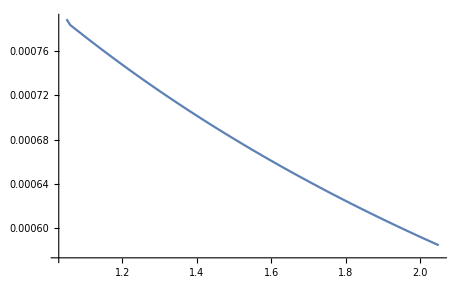

```mathematica
ListPlot[%165,Joined->True]
```

```mathematica
ListPlot[%165,Joined->True,Ticks->{Range[1.2,2,0.4],Range[0.00060,0.00080,0.0001]}(*Ticks->None{{2.2,2.6,3},{0.012,0.014,0.016}}*)(*,FrameTicksStyle->Directive[Large,FontSize->16]*),ImageSize->4*72,LabelStyle->{14,GrayLevel[0]},Background->White,ImageSize->450,AxesLabel->{HoldForm[Subscript[Ε, max]-Subscript[Ε, min]],HoldForm[χ]}]
```

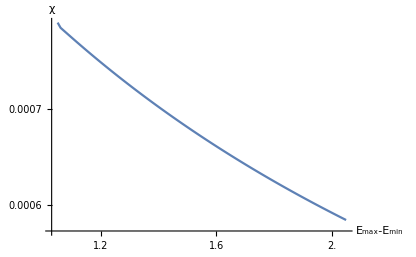

-Graphics-

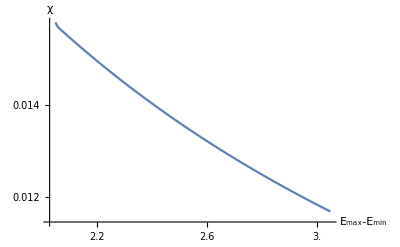

```mathematica
ListLinePlot[%95,Ticks->{Range[2.2,3,0.4],Range[0.012,0.016,0.002]}(*Ticks->None{{2.2,2.6,3},{0.012,0.014,0.016}}*)(*,FrameTicksStyle->Directive[Large,FontSize->16]*),ImageSize->4*72,LabelStyle->{14,GrayLevel[0]},Background->White,ImageSize->450,AxesLabel->{HoldForm[Subscript[Ε, max]-Subscript[Ε, min]],HoldForm[χ]}]
```

```mathematica
DynamicModule[{pt=Scaled[{0.5,0.5}]},ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Detailed",FrameLabel->{{HoldForm[χ[n]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{20.5,GrayLevel[0]},PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1],Epilog->{ Dynamic[Locator[Dynamic[pt,Show[ListPlot[%165,Joined->True,Ticks->{Range[1.2,2,0.4],Range[0.00060,0.00080,0.0001]},ImageSize->4*72,LabelStyle->{14,GrayLevel[0]},Background->White,ImageSize->450,AxesLabel->{HoldForm[Subscript[Ε, max]-Subscript[Ε, min]],HoldForm[χ]}],Background->White,ImageSize->700]]]]}]]
```

```mathematica
Graphics[{First[%144],Inset[%171,Scaled[.4]]},AbsoluteOptions[%144]]
```

Ticks::ticks: {Automatic,Automatic} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

-Graphics-

```mathematica
DynamicModule[{pt=Scaled[{0.5,0.5}]},Plot[Sin[x],{x,0,2 Pi},PlotRange->All,Epilog->{Dynamic[Locator[Dynamic[pt],Plot[Cos[x],{x,0,2 Pi}]]]}]]
```

```mathematica
Clear[ζ]
```

```mathematica
ζ=Import["error4imp.csv"]
```

{{0.0012455,0.00047964,0.000246635,0.000326699,0.00065273,0.00113941,0.00173078,0.00259888,0.0030221,0.00375609,0.00447223},{0.000733525,0.000198104,0.000139596,0.000383845,0.000836792,0.0014504,0.00214592,0.00315613,0.00363552,0.00445143,0.00524628},1997,{0.000375808,0.000266397,0.000580804,0.00114732,0.00189734,0.00275702,0.00368059,0.00492878,0.00546738,0.00643682,0.00735175}}
 |  |  |  |

```mathematica
ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Detailed",FrameLabel->{{HoldForm[χ[n]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{20.5,GrayLevel[0]},PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%77,AxesLabel->{HoldForm[Subscript[Ε, MAX]-Subscript[Ε, MIN]],HoldForm[Χ]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

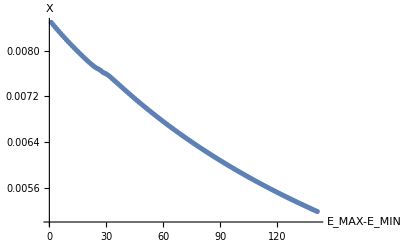

```mathematica
X=%16
```

```mathematica
Show[X,PlotLabel->None]
```

-Graphics-

```mathematica
DynamicModule[{ψψψ=Scaled[{0.5,0.5}]},ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Detailed",FrameLabel->{{HoldForm[Abs[ΔΓ]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{13.5,GrayLevel[0]},PlotRange->All,Epilog->{Dynamic[Locator[Dynamic[ψψψ],Show[%16,Background->White,ImageSize->300]]]}]]
```

```mathematica
λ[ω_,ϵ1_]:=Module[{μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}]},
η:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]];imp5=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.0001-0]]];imp6=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.0001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m=η;ρ2:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"][[ω*100+1]][[2]];ρ3:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"][[ω*100+1]][[2]];ρ4:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"][[ω*100+1]][[2]];ρ5:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"][[ω*100+1]][[2]];ρ6:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"][[ω*100+1]][[2]];ρ7:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"][[ω*100+1]][[2]];ρ8:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"][[ω*100+1]][[2]];ρ9:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp7.csv"][[ω*100+1]][[2]];ρ10:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"][[ω*100+1]][[2]];ρ11:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"][[ω*100+1]][[2]];ρ12:=m-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"][[ω*100+1]][[2]];
list:={ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10,ρ11,ρ12};list]
```

```mathematica
λ[0.42,0.7]
```

{-0.201349,-0.0152011,0.0876129,0.120649,0.141362,0.149254,0.180676,0.14446,0.190491,0.213366,0.23654}

```mathematica
ζζζ=Table[Abs[λ[0.42,0.7]],4000]
```

{{0.203799,0.0176514,0.0851625,0.118199,0.138912,0.146803,0.178226,0.142009,0.188041,0.210915,0.23409},{0.0916184,0.277766,0.38058,0.413616,0.43433,0.442221,0.473644,0.437427,0.483458,0.506333,0.529508},3997,{0.00619126,0.179957,0.282771,0.315807,0.33652,0.344412,0.375834,0.339618,0.385649,0.408524,0.431698}}
 |  |  |  |

```mathematica
Export["error042.dat",%34]
```

error042.dat

```mathematica
Table[{t,Mean[Table[ζζζ⟦x⟧⟦t⟧,{x,1,2000}]],StandardDeviation[Table[ζζζ⟦x⟧⟦t⟧,{x,1,2000}]]},{t,1,11}]
```

{{1,0.36917,0.277862},{2,0.287203,0.212798},{3,0.273986,0.187259},{4,0.274405,0.183463},{5,0.275728,0.1825},{6,0.276471,0.182385},{7,0.2806,0.183489},{8,0.276011,0.182428},{9,0.282373,0.184173},{10,0.287316,0.186449},{11,0.29328,0.189937}}

```mathematica
Export["error042std.dat",%45]
```

error042std.dat

```mathematica
SystemOpen["error042std.dat"]
```

```mathematica
SystemOpen["error042std.dat"]
```

```mathematica
ListPlot[{{4,Around[Table[ζζζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζζζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζζζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζζζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζζζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζζζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζζζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζζζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζζζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζζζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζζζ⟦x⟧⟦11⟧,{x,1,2000}]]}},FrameLabel->{!{HoldForm[Abs[ΔΓ]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{10.5,GrayLevel[0]},PlotStyle->Directive[Black,PointSize[0.03],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Export["deltag.eps",%203]
```

deltag.eps

-Graphics-

```mathematica
ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Detailed",FrameLabel->{{HoldForm[Abs[ΔΓ]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{15.5,GrayLevel[0]},PlotStyle->Directive[Black,PointSize[0.03],"LineOpacity"->1]]
```

-Graphics-

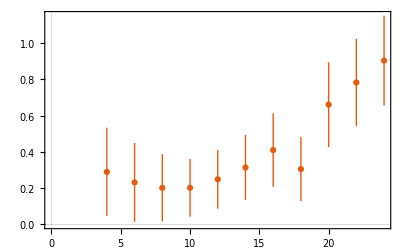

```mathematica
ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Scientific"]
```

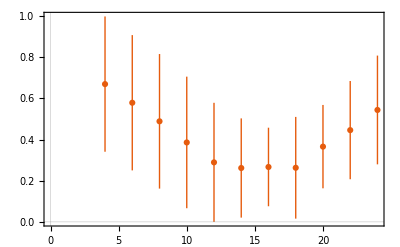

```mathematica
ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Scientific"]
```

```mathematica
Show[%132,Method->{"OptimizePlotMarkers"->True,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

-Graphics-

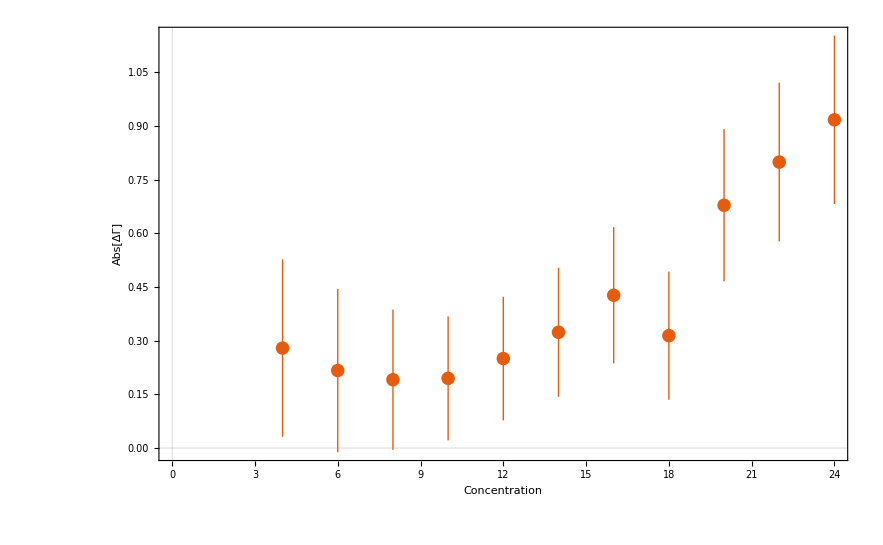

```mathematica
Show[%32,FrameLabel->{{HoldForm[Abs[ΔΓ]],None},{HoldForm[Concentration],None}},PlotLabel->None,LabelStyle->{13,GrayLevel[0]}]
```

```mathematica
λ[1,0.7]
```

{{-0.552197,-0.461492,-0.370012,-0.26079,-0.126339,-0.0202153,0.1044,-0.0324994,0.377422,0.503056,0.626037}}

```mathematica
κ27[ω_]:=κ27[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"][[ω]][[2]]
```

```mathematica
κ37[ω_]:=κ37[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"][[ω]][[2]]
```

```mathematica
κ47[ω_]:=κ47[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"][[ω]][[2]]
```

```mathematica
κ57[ω_]:=κ57[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"][[ω]][[2]]
```

```mathematica
κ67[ω_]:=κ67[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"][[ω]][[2]]
```

```mathematica
κ77[ω_]:=κ77[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"][[ω]][[2]]
```

```mathematica
κ87[ω_]:=κ87[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"][[ω]][[2]]
```

```mathematica
κ97[ω_]:=κ97[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp7.csv"][[ω]][[2]]
```

```mathematica
κ107[ω_]:=κ107[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"][[ω]][[2]]
```

```mathematica
κ117[ω_]:=κ117[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"][[ω]][[2]]
```

```mathematica
κ127[ω_]:=κ127[ω]=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"][[ω]][[2]]
```

```mathematica
κ27[211]
```

1.76604

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_,x_,size_]:=Module[{imp1= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],imp2= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],imp3= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],imp4= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],imp5= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],imp6= Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],imp7=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]]},RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6},size]]
```

```mathematica
DynamicModule[{θ=Scaled[{0.5,0.5}]},ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Detailed",FrameLabel->{{HoldForm[Abs[ΔΓ]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{30.5,GrayLevel[0]},PlotRange->All,PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1],Epilog->{Dynamic[Locator[Dynamic[θ],Show[%171,Background->White,ImageSize->700]]]},ImageSize->2000]]
```